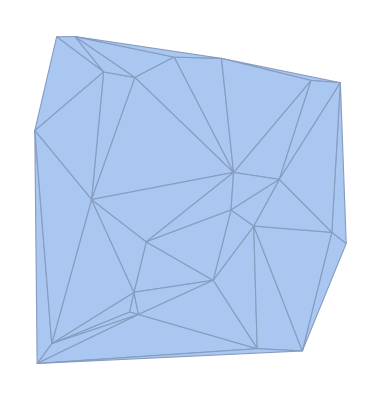

```mathematica
DelaunayMesh[RandomReal[1,{25,2}]]
```

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2}],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"Rainbow",Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"Rainbow",Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"Rainbow",Mesh->None]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{(3+Cos[v]) Cos[u],(3+Cos[v]) Sin[u],Sin[v]},{u,0,2 Pi},{v,0,2 Pi},Mesh->None]
```

-Graphics3D-

```mathematica
Table[Graphics3D[{Yellow,Opacity[.8],PolyhedronData[p,"GraphicsComplex"]}],{p,{"Dodecahedron","Icosahedron","TruncatedIcosahedron"}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Graphics3D[Polygon[{{0,0,0},{1,1,1},{0,1,1},{1,0,0}}]]
```

-Graphics3D-

```mathematica
{Graphics3D[{Yellow,Cylinder[]}],Graphics3D[{Green,Cuboid[{1/2,1/2,1/2}],Blue,Opacity[.4],Cuboid[]}],Graphics3D[{Specularity[White,10],Red,Sphere[]}]}
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Graphics3D[Cylinder[],ViewVector->{{5,-5,5},{5,0,-5}}]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[Sin[x y],{x,0,2 π},{y,0,2 π},Method->{"RotationControl"->method}],{{method,"Globe","Rotation method:"},{"Globe","ArcBall","TrackBall"}}]
```

```mathematica
ContourPlot3D[Cos[x] Sin[y]+Cos[y] Sin[z]+Cos[z] Sin[x]==0,{x,-2 π,2 π},{y,-2 π,2 π},{z,-2 π,2 π},ContourStyle->Directive[FaceForm[Orange,Red],Specularity[White,30]],Mesh->None]
```

-Graphics3D-

```mathematica
SphericalPlot3D[1+Sin[5 ϕ]/5,{θ,0,Pi},{ϕ,0,2 Pi},PlotStyle->Directive[Yellow,Opacity[0.7],Specularity[White,20]],Mesh->None,PlotPoints->30]
```

-Graphics3D-

```mathematica
ChemicalData["Caffeine","MoleculePlot"]
```

-Graphics3D-

```mathematica
KnotData[{"TorusKnot",{3,5}}]
```

-Graphics3D-

```mathematica
ExampleData[{"Geometry3D","Cow"}]
```

-Graphics3D-

```mathematica
Import["ExampleData/747.3ds.gz",ImageSize->Medium]
```

-Graphics3D-

```mathematica
Import["http://www.rcsb.org/pdb/download/downloadFile.do?fileFormat=pdb&compression=NO&structureId=1tf6","PDB",Background->GrayLevel[0.1],ImageSize->Medium]
```

-Graphics3D-

```mathematica
Graphics3D[Table[With[{p={i,j,k}/5},{RGBColor[p],Opacity[.75],Cuboid[p,p+.15]}],{i,5},{j,5},{k,5}]]
```

-Graphics3D-



```mathematica
Graphics[Circle[]]
```

```mathematica
CountryData["France","Population"]
```

64979548 people

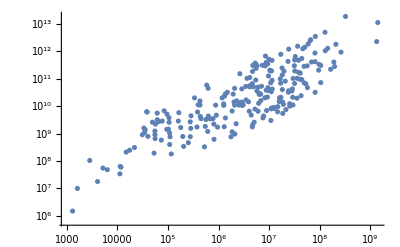

```mathematica
ListLogLogPlot[Tooltip[{CountryData[#,"Population"],CountryData[#,"GDP"]},CountryData[#,"Name"]]&/@CountryData["Countries"]]
```

```mathematica
InteractiveTradingChart[{"GOOGL",{{2009,1,1},{2009,12,31}}}]
```

```mathematica
RandomFunction[
ItoProcess[ⅆx[t]==-x[t] ⅆt+Sqrt[1+x[t]^2] ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],
{0.,5.,0.01}]
```

TemporalData[…]

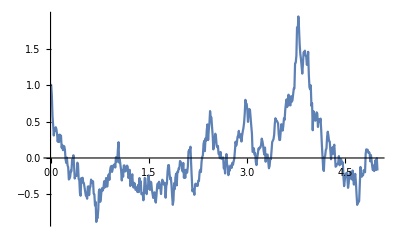

```mathematica
ListLinePlot[%24]
```

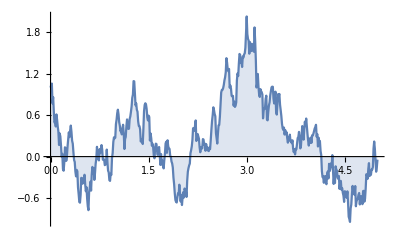

```mathematica
ListLinePlot[
RandomFunction[
ItoProcess[ⅆx[t]==-x[t] ⅆt+Sqrt[1+x[t]^2] ⅆw[t],x[t],{x,1},t,w\[Distributed]WienerProcess[]],
{0.,5.,0.01}], Filling->Axis]
```

```mathematica
Mean[f[x]]
```

Mean[f[x]]

```mathematica
Golly-3.2-Mac
```

-3.2+Golly-Mac

```mathematica
FinancialData["Classes"]
```

{Currencies,Exchanges,ExchangeTradedFunds,Indices,MutualFunds,Sectors,Stocks}

```mathematica
FinancialData["Publishing-Books","Members"]
```

Missing[NotAvailable]

```mathematica
FinancialData["Publishing-Books","]
```

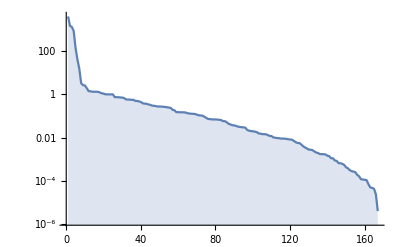

```mathematica
ListLogPlot[Reverse[Sort[Select[Quiet[FinancialData[{#,"USD"}]&/@FinancialData["Currencies"]],NumericQ]]],Filling->Axis,Joined->True]
```

```mathematica
Manipulate[Graphics3D[{Cuboid/@Position[CellularAutomaton[{rn,{2,1},{1,1,1}},If[pr,Normal[SparseArray[Flatten[Table[{16,16,Floor[(53-init)/2]+i}->1,{i,init}],1],{33,33,53}]], {{{Table[1,{init}]}},0}],{{{t}}}],1]},Boxed->False,PlotRange->If[pr,{{0,33},{0,33},{0,53}},All], PlotRangePadding->1,ImageSize->{400,300},SphericalRegion->True], {{rn,14,"rule number"},2,200,4,Appearance->"Labeled"}, {{t,5,"steps"},0,15,1,Appearance->"Labeled"}, {{init,1,"initial height"},1,10,1,Appearance->"Labeled"},Delimiter, {{pr,False,""},{True->"fixed view",False->"zoom to fit"}}, AutorunSequencing->{{1,20},{2,15},{3,10},{4,5}}]
```

```mathematica
Log[x]
```

Log[x]

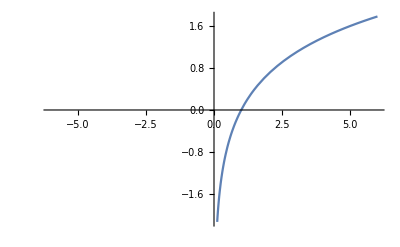

```mathematica
Plot[Log[x],{x,-6,6}]
```

```mathematica
-1/D[Log[x],x]
```

-x

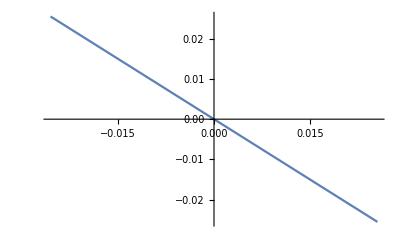

```mathematica
Plot[-x,{x,-0.025500000000000002,0.025500000000000002}]
```

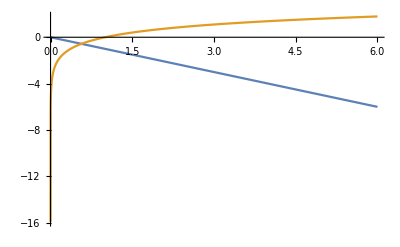

```mathematica
Plot[{-x,Log[x]},{x,0,6}]
```

```mathematica
Integrate[-x, x]
```

-x^2/2

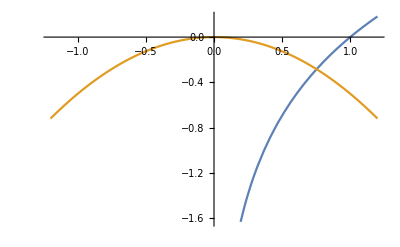

```mathematica
Plot[{Log[x],-x^2/2},{x,-1.2,1.2}]
```

```mathematica
f[x]-Sin[x]/f'[x]
```

f[x]-Sin[x]/f'[x]

```mathematica
With[{f=Identity},
f[x]-Sin[x]/f'[x]]
```

x-Sin[x]

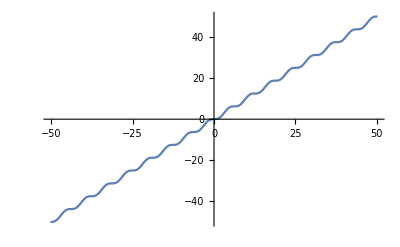

```mathematica
Plot[x-Sin[x],{x,-16 π,16 π}]
```

```mathematica
{x-Sin[x], x+Sin[x]}
```

{x-Sin[x],x+Sin[x]}

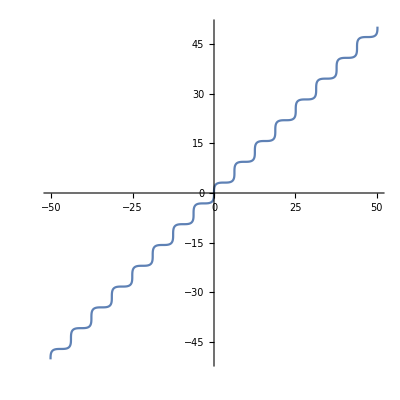

```mathematica
ParametricPlot[{x-Sin[x],x+Sin[x]},{x,-16 π,16 π}]
```

```mathematica
{x+Sin[x]/(-D[x,x]),x-Sin[x]/(-D[x,x])}
```

{x-Sin[x],x+Sin[x]}

```mathematica
{x^2+Sin[x]/(-D[x^2,x]),x^2-Sin[x]/(-D[x^2,x])}
```

{x^2-Sin[x]/(2 x),x^2+Sin[x]/(2 x)}

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

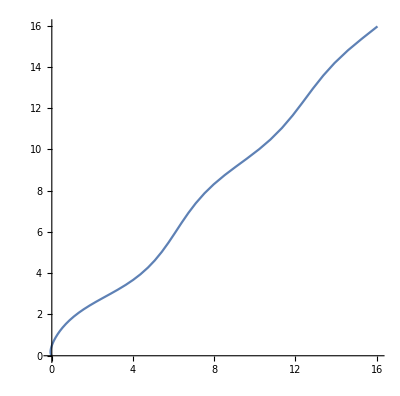

```mathematica
ParametricPlot[{x^2-Sin[x^2]/(2 x),x^2+Sin[x^2]/(2 x)},{x,0,4}]
```

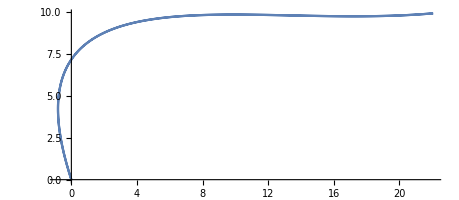

```mathematica
ParametricPlot[{x^2-2x Sin[x],x^2+2x Sin[x]},{x,-4,4}]
```

```mathematica
{x^2-Sin[x]/(2 x),x^2+Sin[x]/(2 x)}
```

{x^2-Sin[x]/(2 x),x^2+Sin[x]/(2 x)}

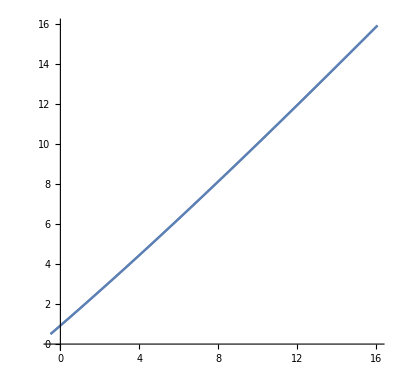

```mathematica
ParametricPlot[{x^2-Sin[x]/(2 x),x^2+Sin[x]/(2 x)},{x,-4,4}]
```

```mathematica
{x-Sin[x], x+Sin[x]}
```

{x-Sin[x],x+Sin[x]}

```mathematica
ParametricPlot[{x-Sin[x],x+Sin[x]},{x,-16 π,16 π}]
```

-Graphics-

```mathematica
{x,x^2}
```

{x,x^2}

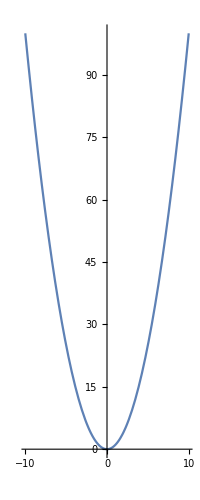

```mathematica
ParametricPlot[{x,x^2},{x,-10,10}]
```

```mathematica
x^2+Sin[x]/(2 x)
```

x^2+Sin[x]/(2 x)

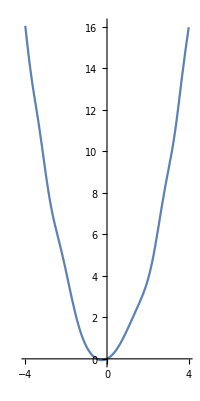

```mathematica
ParametricPlot[{x,x^2+Sin[x^2]/(2 x)},{x,-4,4}]
```

```mathematica
-1/(2x)
```

-1/(2 x)

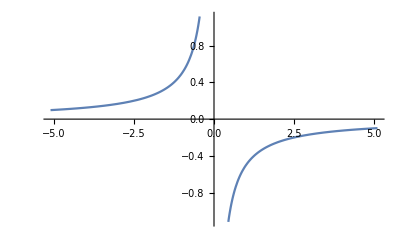

```mathematica
Plot[-1/(2 x),{x,-5.1,5.1}]
```

```mathematica
-x^2/(2x)
```

-x/2

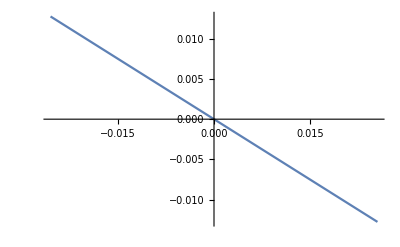

```mathematica
Plot[-x/2,{x,-0.025500000000000002,0.025500000000000002}]
```

```mathematica
Exp[f'[x]/f'[x-1]]
```

ⅇ^(f'[x]/f'[-1+x])

```mathematica
With[{f=#^2&},
ⅇ^(f'[x]/f'[-1+x])]
```

ⅇ^(x/(-1+x))

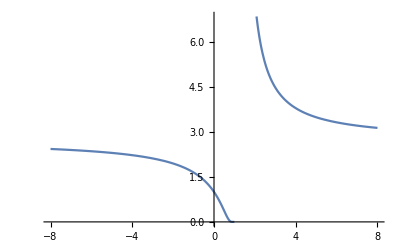

```mathematica
Plot[ⅇ^(x/(-1+x)),{x,-8,8}]
```

```mathematica
With[{f=#^3&},
ⅇ^(f'[x]/f'[-1+x])]
```

ⅇ^(x^2/(-1+x)^2)

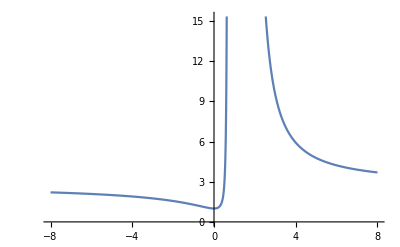

```mathematica
Plot[ⅇ^(x^2/(-1+x)^2),{x,-8,8}]
```

```mathematica
Table[With[{f=#^i&},
ⅇ^(f'[x]/f'[-1+x])], {i, 1, 10}]
```

{ⅇ,ⅇ^(x/(-1+x)),ⅇ^(x^2/(-1+x)^2),ⅇ^(x^3/(-1+x)^3),ⅇ^(x^4/(-1+x)^4),ⅇ^(x^5/(-1+x)^5),ⅇ^(x^6/(-1+x)^6),ⅇ^(x^7/(-1+x)^7),ⅇ^(x^8/(-1+x)^8),ⅇ^(x^9/(-1+x)^9)}

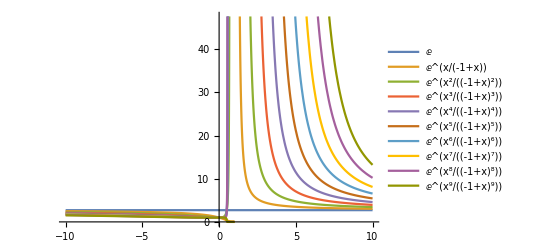

```mathematica
Plot[
{ⅇ,ⅇ^(x/(-1+x)),ⅇ^(x^2/(-1+x)^2),ⅇ^(x^3/(-1+x)^3),ⅇ^(x^4/(-1+x)^4),ⅇ^(x^5/(-1+x)^5),ⅇ^(x^6/(-1+x)^6),ⅇ^(x^7/(-1+x)^7),ⅇ^(x^8/(-1+x)^8),ⅇ^(x^9/(-1+x)^9)}, {x, -10, 10}, PlotLegends->"Expressions"]
```

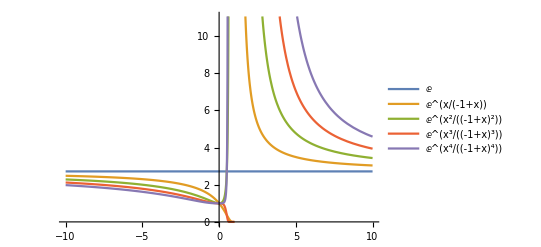

```mathematica
Plot[
{ⅇ,ⅇ^(x/(-1+x)),ⅇ^(x^2/(-1+x)^2),ⅇ^(x^3/(-1+x)^3),ⅇ^(x^4/(-1+x)^4)}, {x, -10, 10}, PlotLegends->"Expressions"]
```

```mathematica
N[Exp[1]]
```

2.71828

```mathematica
Sin[x^2]
```

Sin[x^2]

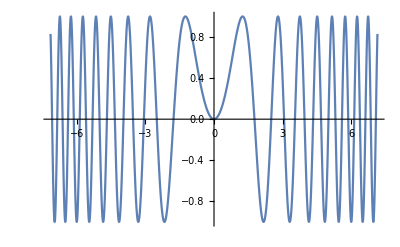

```mathematica
Plot[Sin[x^2],{x,-7.158520453821872,7.158520453821872}]
```

```mathematica
Cos[x^2]
```

Cos[x^2]

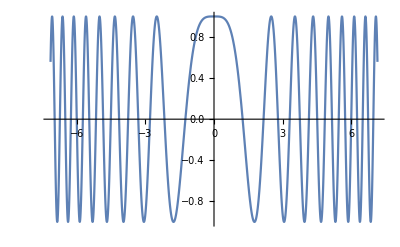

```mathematica
Plot[Cos[x^2],{x,-7.158520453821872,7.158520453821872}]
```

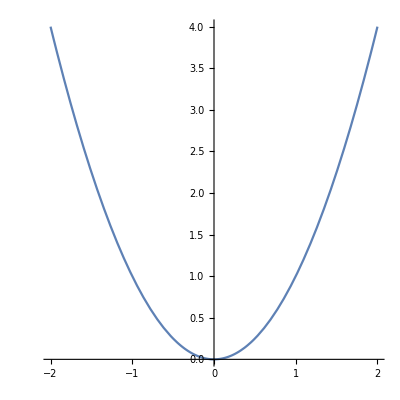

```mathematica
ParametricPlot[
{x, x^2}, {x, -2, 2}]
```

```mathematica
Manipulate[
ParametricPlot[{
{x, x^2}, {x, 2a}
}, {x, -2, 2}],
{a, -1, 1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{
{x, x^2}, {x, 2a(x-a)+a^2}, {x, (x-a)/(-2a)+a^2}
}, {x, -2, 2}],
ListPlot[{{a, a^2}}]
}],
{a, -1, 1}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{
{x, x^2}, {x, 2a(x-a)+a^2}, {x, (x-a)/(-2a)+a^2},
}, {x, -2, 2}],
ListPlot[{{a+b,-b/(2a)+a^2}}]
}],
{{a,-1/2}, -1, 1}, {{b, 0}, -1, 1}]
```

```mathematica
Manipulate[
Show[{
Plot[x, {x, -2, 2}], 
ListPlot[{{a, a}}]}],
{a, -1, 1}]
```

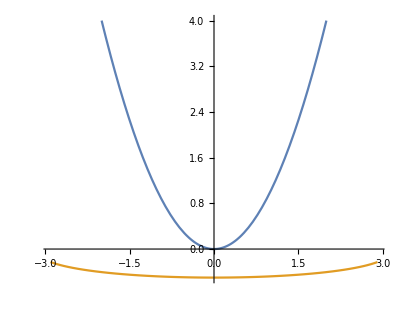

```mathematica
ParametricPlot[{
{x, x^2},{x+Sin[x],-Sin[x]/(2x)}
}, {x, -2, 2}]
```

```mathematica
{a+b,-b/(2a)+a^2}
```

{a+b,a^2-b/(2 a)}

```mathematica
{x+Sin[x],f[x]-Sin[x]/f'[x]}
```

{x+Sin[x],f[x]-Sin[x]/f'[x]}

```mathematica
With[{f=#^2&},
{x+Sin[x],f[x]-Sin[x]/f'[x]}]
```

{x+Sin[x],x^2-Sin[x]/(2 x)}

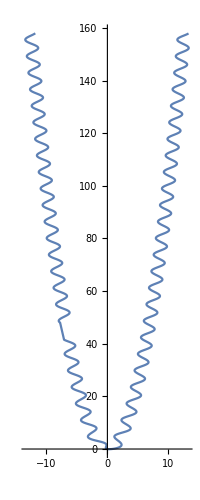

```mathematica
ParametricPlot[{x+Sin[x^2],x^2-Sin[x^2]/(2 x)},{x,-4 π,4 π}]
```

```mathematica
With[{f=#^2&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[x^2],x^2-Sin[x^2]/(2 x)}

```mathematica
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}
```

{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}

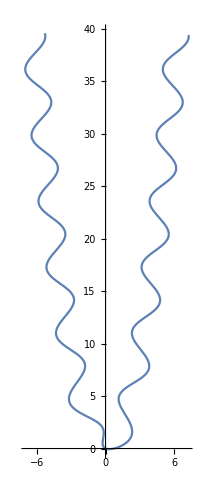

```mathematica
ParametricPlot[{x+Sin[x^2],x^2-Sin[x^2]/(2 x)},{x,-2 π,2 π}]
```

```mathematica
With[{f=#^3&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[x^3],x^3-Sin[x^3]/(3 x^2)}

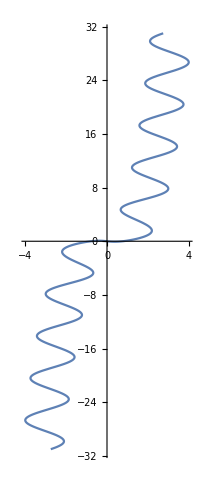

```mathematica
ParametricPlot[{x+Sin[x^3],x^3-Sin[x^3]/(3 x^2)},{x,-π,π}]
```

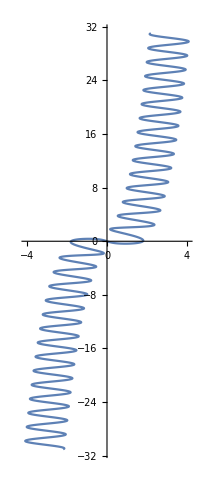

```mathematica
ParametricPlot[{x+Sin[3 x^3],x^3-Sin[3 x^3]/(3 x^2)},{x,-π,π}]
```

```mathematica
With[{f=Exp},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[ⅇ^x],ⅇ^x-ⅇ^-x Sin[ⅇ^x]}

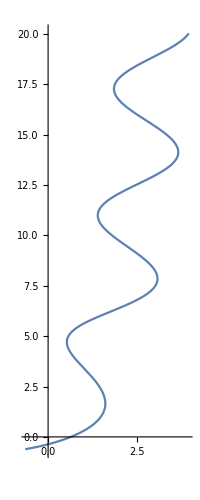

```mathematica
ParametricPlot[{x+Sin[ⅇ^x],ⅇ^x-ⅇ^-x Sin[ⅇ^x]},{x,-1,3}]
```

```mathematica
{x+Sin[f[x]]/.f[x]->Cos[x],f[x]-Sin[f[x]]/f'[x]/.f->Sin}
```

{x+Sin[Cos[x]],Sin[x]-Sec[x] Sin[Sin[x]]}

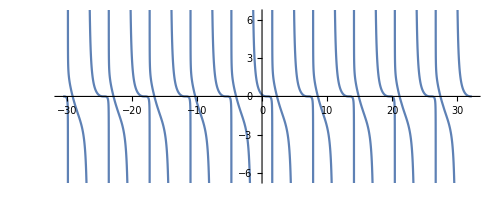

```mathematica
ParametricPlot[{x+Sin[Cos[x]],Sin[x]-Sec[x] Sin[Sin[x]]},{x,-10 π,10 π}]
```

```mathematica
With[{f=Identity},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[x],x-Sin[x]}

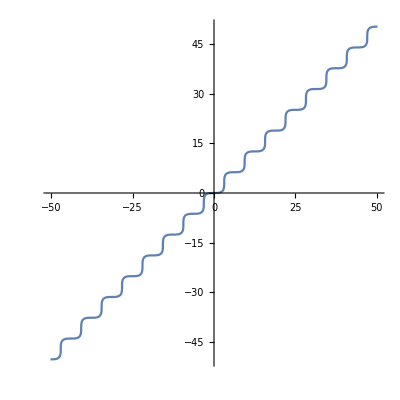

```mathematica
ParametricPlot[{x+Sin[x],x-Sin[x]},{x,-16 π,16 π}]
```

```mathematica
{x+Sin[f[x]],f[x]-Sin[f[x]]/(f^′)[x]}
```

```mathematica
{x+Sin[x],x-Sin[x]}
```

```mathematica
{x+Sin[f[x]]/.f[x]->x+Sin[x],f[x]-Sin[f[x]]/f'[x]/.{f[x]->x-Sin[x], f'[x]->D[x-Sin[x],x]}}
```

{x+Sin[x+Sin[x]],x-Sin[x]-Sin[x-Sin[x]]/(1-Cos[x])}

Power::infy: Infinite expression 1/0. encountered.

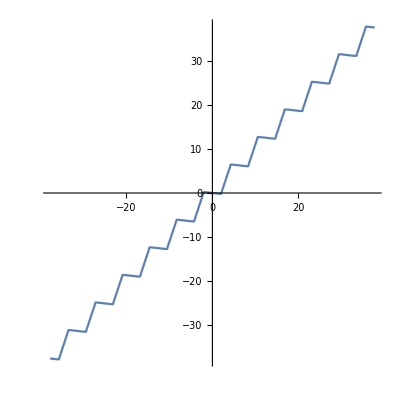

```mathematica
ParametricPlot[{x+Sin[x+Sin[x]],x-Sin[x]-Sin[x-Sin[x]]/(1-Cos[x])},{x,-37.69911184307752,37.69911184307752}]
```

```mathematica
With[{f=Log},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[Log[x]],Log[x]-x Sin[Log[x]]}

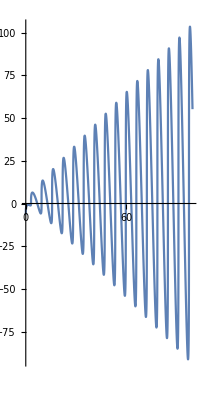

```mathematica
ParametricPlot[{x+Sin[x],Log[x]-x Sin[x]},{x,0,100}]
```

```mathematica
With[{f=√(#^2+1)&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[√(1+x^2)],√(1+x^2)-(√(1+x^2) Sin[√(1+x^2)])/x}

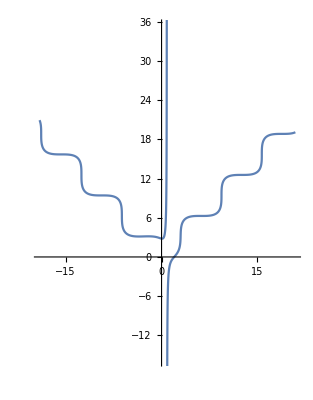

```mathematica
ParametricPlot[{x+Sin[√(1+x^2)],√(1+x^2)-(√(1+x^2) Sin[√(1+x^2)])/x},{x,-20,20}]
```

```mathematica
With[{f=√#&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[√x],√x-2 √x Sin[√x]}

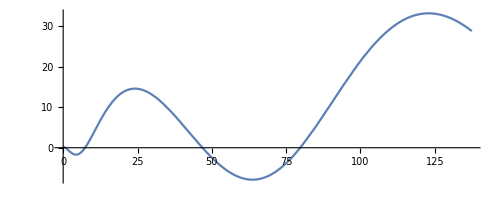

```mathematica
ParametricPlot[{x+Sin[√x],√x-2 √x Sin[√x]},{x,-98.69604401089359,138.174461615251}]
```

```mathematica
With[{f=Sin},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[Sin[x]],Sin[x]-Sec[x] Sin[Sin[x]]}

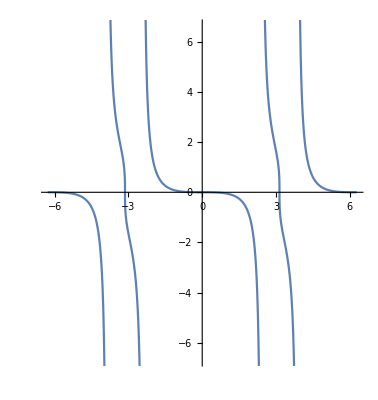

```mathematica
ParametricPlot[{x+Sin[Sin[x]],Sin[x]-Sec[x] Sin[Sin[x]]},{x,-2π,2 π}]
```

```mathematica
With[{f=#^3+#^2+#&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[x+x^2+x^3],x+x^2+x^3-Sin[x+x^2+x^3]/(1+2 x+3 x^2)}

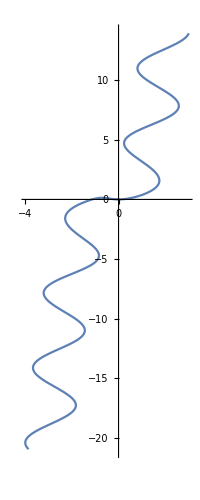

```mathematica
ParametricPlot[{x+Sin[x+x^2+x^3],x+x^2+x^3-Sin[x+x^2+x^3]/(1+2 x+3 x^2)},{x,-3,2}]
```

```mathematica
x/(√(x+1))
```

x/(√(1+x))

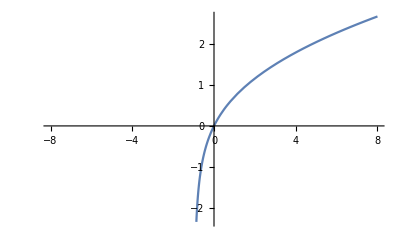

```mathematica
Plot[x/(√(1+x)),{x,-8,8}]
```

```mathematica
x/(√(1+x^2))
```

x/(√(1+x^2))

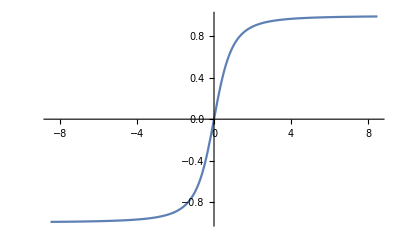

```mathematica
Plot[x/(√(1+x^2)),{x,-8.493333333333334,8.493333333333334}]
```

```mathematica
FullSimplify[
Normalize[D[{x,x/(√(1+x^2))},x]].
Normalize[D[{x,CDF[NormalDistribution[],x]},x]], Element[x,Reals]]
```

(1+ⅇ^(x^2/2) √(2 π) (1+x^2)^(3/2))/(√((1+2 ⅇ^(x^2) π) (2+3 x^2+3 x^4+x^6)))

```mathematica
With[{f=#/(√(1+#^2))&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[x/(√(1+x^2))],x/(√(1+x^2))-Sin[x/(√(1+x^2))]/(-x^2/((1+x^2)^(3/2))+1/(√(1+x^2)))}

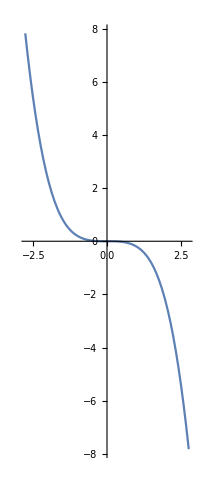

```mathematica
ParametricPlot[{x+Sin[x/(√(1+x^2))],x/(√(1+x^2))-Sin[x/(√(1+x^2))]/(-x^2/((1+x^2)^(3/2))+1/(√(1+x^2)))},{x,-2,2}]
```

```mathematica
With[{f=(1+ⅇ^(#^2/2) √(2 π) (1+#^2)^(3/2))/(√((1+2 ⅇ^(#^2) π) (2+3 #^2+3 #^4+#^6)))&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[(1+ⅇ^(x^2/2) √(2 π) (1+x^2)^(3/2))/(√((1+2 ⅇ^(x^2) π) (2+3 x^2+3 x^4+x^6)))],(1+ⅇ^(x^2/2) √(2 π) (1+x^2)^(3/2))/(√((1+2 ⅇ^(x^2) π) (2+3 x^2+3 x^4+x^6)))-Sin[(1+ⅇ^(x^2/2) √(2 π) (1+x^2)^(3/2))/(√((1+2 ⅇ^(x^2) π) (2+3 x^2+3 x^4+x^6)))]/((3 ⅇ^(x^2/2) √(2 π) x √(1+x^2)+ⅇ^(x^2/2) √(2 π) x (1+x^2)^(3/2))/(√((1+2 ⅇ^(x^2) π) (2+3 x^2+3 x^4+x^6)))-((1+ⅇ^(x^2/2) √(2 π) (1+x^2)^(3/2)) ((1+2 ⅇ^(x^2) π) (6 x+12 x^3+6 x^5)+4 ⅇ^(x^2) π x (2+3 x^2+3 x^4+x^6)))/(2 (1+2 ⅇ^(x^2) π) (2+3 x^2+3 x^4+x^6) √((1+2 ⅇ^(x^2) π) (2+3 x^2+3 x^4+x^6))))}

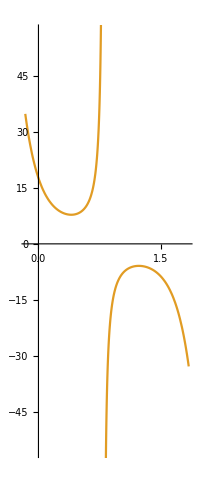

```mathematica
ParametricPlot[%188,{x,-1,1}]
```

```mathematica
With[{f=#^2&},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[x^2],x^2-Sin[x^2]/(2 x)}

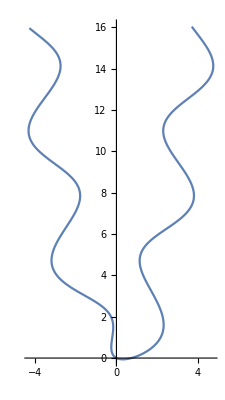

```mathematica
ParametricPlot[{x+Sin[x^2],x^2-Sin[x^2]/(2 x)},{x,-4,4}]
```

```mathematica
With[{f=Identity},
{x+Sin[f[x]],f[x]-Sin[f[x]]/f'[x]}]
```

{x+Sin[x],x-Sin[x]}

```mathematica
ParametricPlot[{x+Sin[x],x-Sin[x]},{x,-16 π,16 π}]
```

-Graphics-

```mathematica
{x[t]==t+Sin[t],y[t]==t-Sin[t]}
```

{x[t]==t+Sin[t],y[t]==t-Sin[t]}

```mathematica
Sin[x]^2
```

Sin[x]^2

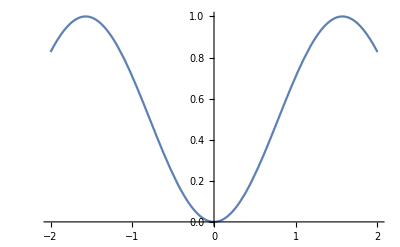

```mathematica
Plot[Sin[x]^2,{x,-2,2}]
```

```mathematica
-Sin[x]^2
```

-Sin[x]^2

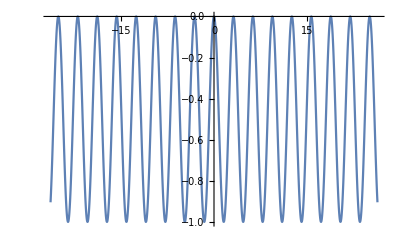

```mathematica
Plot[-Sin[x]^2,{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
-Sin[x]^2+1
```

1-Sin[x]^2

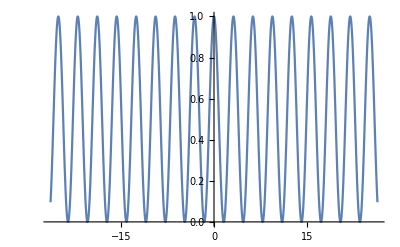

```mathematica
Plot[1-Sin[x]^2,{x,-26.389378290154262,26.389378290154262}]
```

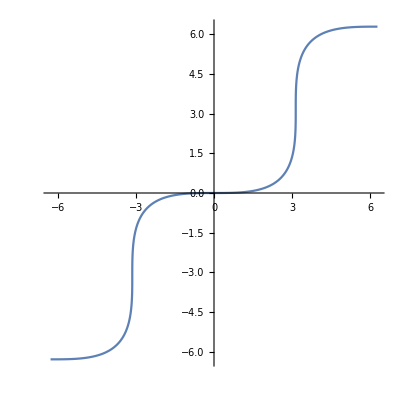

```mathematica
ParametricPlot[{x+Sin[x],x-Sin[x]},{x,-2π,2 π}]
```

```mathematica
ParametricPlot[
{x+Sin[x],x-Sin[x]},
{x,-2π,2 π}]
```

```mathematica
D[{x+Sin[x],x-Sin[x]},x]
```

{1+Cos[x],1-Cos[x]}

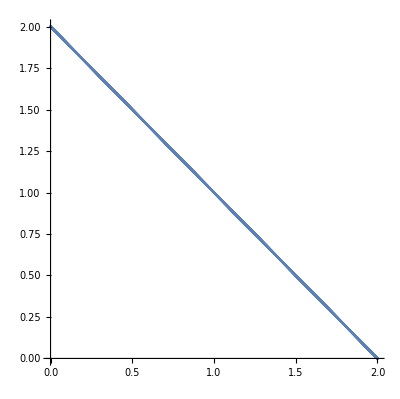

```mathematica
ParametricPlot[{1+Cos[x],1-Cos[x]},{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Manipulate[
Show[{
ParametricPlot[{
{x, x^2}, {x, 2a(x-a)+a^2}, {x, (x-a)/(-2a)+a^2}
}, {x, -2, 2}],
ListPlot[{{a+b,-b/(2a)+a^2}}]
}],
{{a,-1/2}, -1, 1}, {{b, 0}, -1, 1}]
```

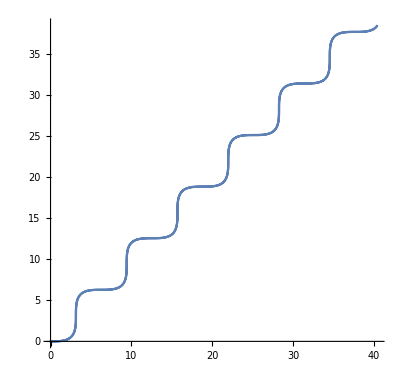

```mathematica
ParametricPlot[
{x^2+Sin[x^2],x^2-Sin[x^2]},
{x,-2π,2 π}]
```

```mathematica
1+1
```

2